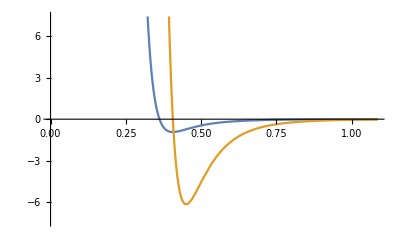

```mathematica
(* Lennard-Jones potential:
U(r)=4ϵ[(σ/r)^12-(σ/r)^6] *)
u[r_]:=4*epsilon*((sigma/r)^12-(sigma/r)^6);
f[r_]:=Evaluate[-D[u[r],r]];
epsilon=0.929;
sigma=0.362;
Plot[{u[r],f[r]},{r,0.1*sigma,3*sigma},PlotRange->{-8*epsilon,8*epsilon}]
```

```mathematica
(* y=∫f'(x)ⅆx anti-derivative *)
Integrate[x^2,x]
```

x^3/3

```mathematica
Integrate[Cos[x],x]
```

Sin[x]

```mathematica
f[x_]:=1/x;
Integrate[f[x],x]
```

Log[x]

```mathematica
Integrate[ArcTan[x],x]
```

x ArcTan[x]-1/2 Log[1+x^2]

```mathematica
∫ArcSin[x]ⅆx
```

√(1-x^2)+x ArcSin[x]

```mathematica
Integrate[Cos[x^2],x]
```

√(π/2) FresnelC[√(2/π) x]

```mathematica
?FresnelC
```

FresnelC[z] gives the Fresnel integral C(z).

```mathematica
∫√ArcTan[x] ⅆx
```

∫√ArcTan[x]ⅆx

```mathematica
Integrate[1-x^2,x]
```

x-x^3/3

```mathematica
Integrate[1-x^2,{x,0,3}]
```

-6

```mathematica
∫_0^(2*Pi) (Sin[x])^2ⅆx
```

π

```mathematica
∫_(-∞)^∞ E^(-a*x^2)ⅆx
```

ConditionalExpression[(√π)/(√a),Re[a]>0]

```mathematica
Integrate[E^(-a*x^2),{x,-Infinity,Infinity},Assumptions->{a>0}]
```

(√π)/(√a)

```mathematica
Assuming[a>0,Integrate[E^(-a*x^2),{x,-Infinity,Infinity}]]
```

(√π)/(√a)

```mathematica
∫1/xⅆx
```

Log[x]

```mathematica
∫_1^∞ (1/x)ⅆx
```

Integrate::idiv: Integral of 1/x does not converge on {1, ∞}.

∫_1^∞ 1/x ⅆx

```mathematica
f[t_]:=a+b*t+c*t^2;
∫_0^t f[x]ⅆx
```

a t+(b t^2)/2+(c t^3)/3

```mathematica
NIntegrate[Sqrt[ArcTan[x]],{x,0,1}]
```

0.629823

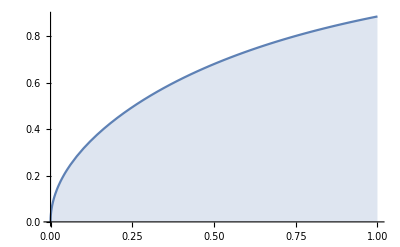

```mathematica
Plot[Sqrt[ArcTan[x]],{x,0,1},Filling->Axis]
```

```mathematica
(* dW=-pdV
vdW:P=nRT/(V-nb)-a(n/V)^2 
Tell mathematica waht u konw: assumptions *)
p[v_]:=n*r*t/(v-n*b)-a*(n/v)^2;
w=Integrate[p[v],{v,v1,v2}]
```

ConditionalExpression[-(n (a n+r t v1 Log[-b n+v1]))/v1+(n (a n+r t v2 Log[-b n+v2]))/v2,((Im[v1]≥Im[v2]&&(Im[v1]≤Im[n] Re[b]+Im[b] Re[n]||Im[v2]≥Im[n] Re[b]+Im[b] Re[n]||Im[v2] Re[b] Re[n]+Im[n] Re[b] Re[v1]+Im[b] (Im[n] (Im[v1]-Im[v2])+Re[n] (Re[v1]-Re[v2]))+Im[v1] (-Re[b] Re[n]+Re[v2])≥Im[v2] Re[v1]+Im[n] Re[b] Re[v2]))||(Im[v1]≤Im[v2]&&(Im[v1]≥Im[n] Re[b]+Im[b] Re[n]||Im[v2]≤Im[n] Re[b]+Im[b] Re[n]||Im[v2] Re[b] Re[n]+Im[n] Re[b] Re[v1]+Im[b] (Im[n] (Im[v1]-Im[v2])+Re[n] (Re[v1]-Re[v2]))+Im[v1] (-Re[b] Re[n]+Re[v2])≤Im[v2] Re[v1]+Im[n] Re[b] Re[v2])))&&((Re[v1/(-v1+v2)]≥0&&v1≠0&&v1^2≠v1 v2)||v1/(v1-v2)∉Reals||Re[v1/(v1-v2)]>1)&&(((Re[(b n-v1)/(v1-v2)]<-1||(b n-v1)/(v1-v2)∉Reals)&&(Re[(-b n+v1)/(v1-v2)]==0||Re[(-b n+v1)/(v1-v2)]≥1))||(Re[(b n-v1)/(v1-v2)]≥0&&(Re[(-b n+v1)/(v1-v2)]<0||(b n-v1)/(v1-v2)∉Reals))||(-b n+v1)/(v1-v2)∉Reals)]

```mathematica
assumptions={v1>0,v2>0,n>0,t>0,r>0,a>0,b>0,v1>n*b,v2>n*b,v2>v1};
Assuming[assumptions,Integrate[-p[v],{v,v1,v2}]]
```

n (a n (1/v1-1/v2)+r t (Log[-b n+v1]-Log[-b n+v2]))

```mathematica
(* P-I-B
Subscript[ψ, n](x)=Asin(nπx/L),A is Norm. const.;
∫_0^L (|Subscript[ψ, n]|)^2 ⅆx=1=A^2∫_0^L (sin(nπx/L)^2 ⅆx *)
f[x_]:=Sin[n*Pi*x/l];
a=Sqrt[1/Assuming[n∈Integers,Integrate[(f[x])^2,{x,0,l}]]]
```

√2 √(1/l)